# Video Traking

User interface for video traking by Karolis Misiunas. 
Warning: The routine works slightly differently on Mac and Windowns since M9+ because FFmpeg library is not compatable.

ToDo:
 - [ ] Add multiple ROI processing in UI
 - [ ] Reporting: Running analysis reporting as Monitor[]
 - [ ] FFmpeg: optimise for speed (it is not a bottle neck, but would be nice to have additional ~15%
 - [ ] Processing: run on multiple cores - will speed it up a lot!
 - [ ] Localised intensity correction for treshhold
 - [ ] FFImport frame count is not working properly or relies on Import[]
 - find out what happens when there is poor particle and a good one in intire analysis - might be we include them as singles?!

```mathematica
Quit[];
```

```mathematica
<<VideoAnalysis`
<<Linking`
$HistoryLength = 2; (*prevent memory overload*)
SetOptions[FFmpeg, 
  "Colors"->1 (*number of color channels*),
  "ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
];
SetOptions[VideoIO,
  "FrameIdFromFrame"-> True,
  "Import" -> FFImport
];
```

## Under the hood functions

```mathematica
FindIntervals[raw_]:= Module[{list},
  list = Sort[ DeleteDuplicates[raw]];
  If[ Length[list] == 0, Return[{}]]; 
  Append[ 
  Reap[FoldList[
    If[#2-Last[#1]==1,
      Append[#1,#2],
      If[Length[#1]==1, Sow[First[#1]], Sow[Interval[{First[#1],Last[#1]}]]];
      {#2}] & ,
    {First[raw]},
    Rest[list]]][[-1,1]],Last[list] 
  ] 
];

processVideo[file_] := Module[{loadTime, analysisTime,oldROI,outputFolder, problems},
  Clear[output];
  oldROI = ROICurrent[] ; (*reuse ROI*)
  Print@Style["===================== " ~~ FileNameTake[file] ~~" =====================", Orange];

  (* === Analyse === *)
  VideoSelect[ file ];
  ROISelect[ oldROI ];
  loadTime = First@AbsoluteTiming[ VideoBufferAll[] ];
  BackgroundUpdate[];
  (*BackgroundUpdate@bgAssociation[ VideoFile[]];*)
  {analysisTime,output} = AbsoluteTiming @ VideoAnalyse[];

  (* === Report === *)
  problems = VideoProblemInFrames[]⟦;;,1⟧;
  Print[ "Analysis took (load + recognition): "<> ToString@loadTime <> " + "<> ToString@analysisTime<>" = "<> ToString@(loadTime+analysisTime)<>" sec"];
  Print["Particles found: " ,Style[Length[output], Green], ", and problems were in ", Style[Length[problems], Red] , " frames"];
  (*show detection frequancy*)
  (*Print @ NumberLinePlot[
    { (*FindIntervals[output⟦All, 1⟧],*) FindIntervals[problems]},
    ImageSize->Full
  ];*)
  (* show background and a selection of bad frames *)
  Print @ Grid[ Partition[
    {Column[{"Background", BackgroundCurrent[]}]}   ~Join~
   If[Length[problems]>1,(Column[{Style[#, Red], VideoGet[#]}] &/@ Sort@RandomChoice[problems,14] ), {}]
  , 5]];
  

  (* === Post Process === *)

  (* mark frames with problems as LQPos *)
  (output⟦#,5⟧ = 0)&/@Position[output⟦;;,1⟧ , _Integer?(MemberQ [problems, #]&)]; 
  (*update time and positions to absolute ones*)
  cornerPos = ROICurrent[]⟦1⟧;
  output⟦All,1⟧ = VideoFrameID /@ output⟦All,1⟧ ; (*time*)
  output⟦All,2⟧ = output⟦All,2⟧ + cornerPos⟦1⟧ ; (*x*)
  output⟦All,3⟧ = output⟦All,3⟧ + cornerPos⟦2⟧ ; (*y*)
  (* save to file *)
  outputFolder = FileNameJoin[{DirectoryName[file],"raw_points"}];
  If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

  Print["Done: "<>
  ToString@Export[ FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  output]];
]
```

#### Backgroud pre-computation

```mathematica
(* Input: must be structured file names *)
(* Returns: "bgAssociation" association: file -> background img *)
(* Warning this is less efficiant than default method*)
prepareBackgroundImages[filesAll_, clusterSize_] := Module[
  {clusters, processCluster, roi,  getAllImages},
  roi = ROICurrent[];
  clusters = Partition[filesAll, clusterSize, clusterSize,{1,1},{}];
  (*special case*)
  If[Length @ Last @ clusters < clusterSize,  (* attach to the last cluster*)
    clusters = Append[clusters⟦;;-3⟧, Join[clusters⟦-1⟧,clusters⟦-2⟧]];
  ];

  processCluster[files_]:= Module[
	{allImages, selectedImages},
	allImages = Select[ImageQ] @ Flatten[getAllImages/@files];
	selectedImages = RandomSample[allImages, 20000];
	Image[Median[ImageData/@ selectedImages ]] (*median algorithm*)
  ];

  (* obtain all images *) 
  getAllImages[file_] := Module[{},
	VideoSelect[file];
	ROISelect[roi];
    VideoBufferAll[];
	VideoGet /@ Range[VideoLength[]]
  ];

  Print["Pre-computing background images for ", Length[filesAll], " files"];
  Monitor[
	bgImages = Table[
		(Print["Cluter ", i, " → ", #]; #) &@  processCluster[clusters⟦i⟧] ,
		{i, 1, Length[clusters]}
	],
	Row[{"Analysing clusters: ",ProgressIndicator[i,{1,Length[clusters]}],i}," "]
  ];
  
  bgAssociation = Join @@ Table[
		AssociationMap[ bgImages⟦i⟧ &, clusters⟦i⟧ ] ,
		{i, 1, Length[clusters]}
	];
  Print["Finised analysing all the backround images"];
];
```

## Step 1 - Select sample video file

```mathematica
VideoSelect["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/200fps_s4.avi"]
```

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

VideoAddProcessRawFrame: new function count is 1

200fps_s4.avi has 10000 frames and is 400x500

## Step 2 - Select region of intrest

```mathematica
ROISelect[]
```

(0 | 0
400 | 500)

```mathematica
ROISelect[({{57, 364}, {375, 444}})]
```

(57 | 364
375 | 444)

## Step 3 - Configure tracing algorithm

```mathematica
Options[VideoTracking];

(* Light Particles *)
SetOptions[VideoTracking, 
"FilterElongation" -> {0.0, 0.6},
 "FilterArea" -> {8,33},
 "UpdateBackgroung" -> False,
 Threshold -> 0.1,
"ForegroundMethod"->"Bright" 
];
```

```mathematica
(* Dark Particles *)
SetOptions[VideoTracking, 
 "FilterElongation" -> {0.0, 0.4},
 "FilterArea" -> {12,38},
 "UpdateBackgroung" -> False,
 Threshold -> 0.22,
"ForegroundMethod"->"Dark" 
];
```

## Step 4 - Test configuration

```mathematica
VideoBufferAll[]
```

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

Part::partd: Part specification 753714⟦753715⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 10000 in 753714⟦753715⟧.

```mathematica
VideoGet[20000]
```

-Graphics-

```mathematica
VideoFindThreshold[]
```

```mathematica
BackgroundUpdate[]
```

-Graphics-

```mathematica
findFrameNo[frameId_]:= Which[
VideoFrameID[1] ≤  frameId ≤ VideoFrameID[VideoLength[]], 
	frameId - VideoFrameID[1]+1,
frameId > VideoFrameID[VideoLength[]],
	Print["Go forward by ",N[(frameId - VideoFrameID[1])/VideoLength[]], " vidoes"],
VideoFrameID[1] >  frameId ,
	Print["Go back by ",N[-(frameId - VideoFrameID[1])/VideoLength[]+1], " vidoes"]
];
```

#### Analyse Single Frame

(1965 | 42.039 | 55.574 | 0. | 1. | 1.219 | 2.429 | 0.108
1965 | 297.043 | 43.526 | 0. | 1. | 2.152 | 0.137 | 0.132
1965 | 39.289 | 39.431 | 0. | 1. | 1.427 | 2.278 | 0.117
1965 | 227.87 | 35.731 | 0. | 1. | 1.098 | 1.013 | 0.118)

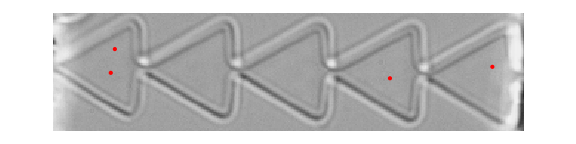
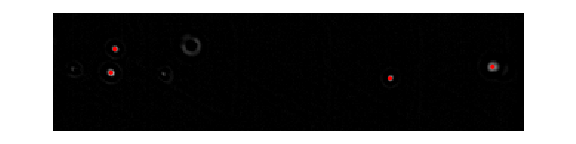
-Graphics--Graphics--Graphics--Graphics-

Area→{1→1.,2→12.375,3→29.625,4→19.625,5→1.,6→12.375}

Elongation→{1→0.,2→0.2368,3→0.0732786,4→0.146263,5→0.,6→0.128682}

FindThreshold→0.193413

```mathematica
frame =1 60 30         +17 30           -40+100;
frame = 1865+100;
If[!IntegerQ[frame]|| 0>=frame||frame >  VideoLength[], frame = 1; Print@"Frame out of range. set to 1."];
ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list[[;;,{2,3}]]},ImageSize->Large]

curPos = VideoAnalyseFrame[frame]
Row[{
ShowTrackOverlayed[ VideoGet[frame] , curPos],
ShowTrackOverlayed[ BackgroundCurrent[], curPos],
ShowTrackOverlayed[ VideoGetForeground@VideoGet[frame] , curPos] ,
ShowTrackOverlayed[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] , curPos]
}]

"Area"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Area"]

"Elongation"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Elongation"]
"FindThreshold"-> FindThreshold@VideoGetForeground@VideoGet[frame]
```

## Step 5 - Select file range and run analysis

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[1]]
```

```mathematica
analyseTheseFiles=Select[
(StringReplace[VideoFile[], RegularExpression["\\d+.avi"]-> ""]~~ToString@#~~".avi")&/@ ({4})
,
FileExistsQ];
```

```mathematica
analyseTheseFiles
```

{/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/200fps_s4.avi}

#### Background computation (optional)

```mathematica
BackgroungUpdate@bgAssociation[ VideoFile[]]
```

-Graphics-

```mathematica
DumpSave["background_images.mx", bgAssociation];
```

```mathematica
prepareBackgroundImages[analyseTheseFiles, 4]
```

Pre-computing background images for 26 files

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

VideoAddProcessRawFrame: new function count is 1

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

General::stop: Further output of FFImport :: notSupported will be suppressed during this calculation.

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

Cluter 1 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 2 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 3 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 4 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 5 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«3 more identical outputs»

Cluter 6 → -Graphics-

Finised analysing all the backround images

#### Run the analysis

```mathematica
Monitor[
Do[ processVideo[analyseTheseFiles⟦i⟧], {i, Length[analyseTheseFiles] }],
Row[{"Analysing files: ",ProgressIndicator[i,{1,Length[analyseTheseFiles]}],i}," "]
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "video_tracking_paramters.txt"}]     ,
ToString@{
"ROI" -> ToString@ROICurrent[],
"VideoTracking" ->Options[VideoTracking]
}
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "sample_frame.png"}]     ,
FFImport[VideoFile[], {"Frames", 1}]
];
```

===================== 200fps_s4.avi =====================

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

VideoAddProcessRawFrame: new function count is 1

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 45.4207 + 560.527 = 605.948 sec

Particles found: 16414, and problems were in 25 frames

Background
-Graphics- | 1427
-Graphics- | 1432
-Graphics- | 1432
-Graphics- | 2270
-Graphics-
2270
-Graphics- | 2291
-Graphics- | 2292
-Graphics- | 2292
-Graphics- | 2294
-Graphics-
2294
-Graphics- | 2295
-Graphics- | 2296
-Graphics- | 2962
-Graphics- | 2962
-Graphics-

Done: /Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/200fps_s4.csv

/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/video_tracking_paramters.txt

#### Combining the two points

```mathematica
white = Import["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/200fps_s4_white.csv"];
dark = Import["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/200fps_s4_dark.csv"];

points = SortBy[ white ~ Join~ dark, First];
```

```mathematica
points[[1,1]]//Head
```

Integer

```mathematica
?VideoReadFrameID
```

VideoReadFrameID[image_] returns video frame ID from 4 pixels in top right corrner of a frame

```mathematica
?VideoFrameID
```

VideoFrameID[no_(optional)] returns id of a frame or full list of them. 
  (if there was none set by video will give 1..VideoLength[])

```mathematica
minId = VideoReadFrameID@VideoGet[1]
```

753714

```mathematica
i = 0;
Select[points, #[[1]]==minId+i&]⟦All, {2,3}⟧
```

(91.16 | 423.721
175.258 | 389.358
202.074 | 410.879)

```mathematica
Manipulate[
Show[
VideoGet[i],
Graphics[{Red} ~ Join~ (Point/@Select[points, #[[1]]==minId+i&]⟦All, {2,3}⟧) ]
],
{i, 1, 7000, 1}
]
```

```mathematica
Export["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/joined.csv", points]
```

/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/joined.csv

```mathematica
<< KLabTracking`
```

```mathematica
tracks = Import[ "/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/tracks/joined.json", "KLab"]
```

KLab: Imported Track Assembly
time→Sun 19 Jun 2016 19:38:32GMT+1.
experiment→from: /Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/raw_points/joined.csv
comment→
units→{frame,px_x,px_y,px_z}
array_format→{time_stamp,x,y,z(optional),param(optional)}
number→531

<|1→{{753714.,175.258,389.358,0.,1.,1.291,1.641,0.267},{753715.,174.783,388.925,0.,0.},{753716.,174.307,388.492,0.,1.,1.229,1.618,0.237},3,{753720.,173.759,389.515,0.,1.,1.149,0.081,-0.207},{753721.,174.862,389.708,0.,1.,1.167,1.656,0.258},{753722.,174.038,389.984,0.,1.,1.137,1.664,0.205}},529,720→{{1},12,{1}}|>
 |  |  |  |

```mathematica
drawTrack[t_][id_ -> track_] := {ColorData[97,id] , Line[ Select[ track, First[#] ≤ t &] [[All, {2,3}]]  ]} ;
```

```mathematica
Flatten@Map[ drawTrack[4+minId],Normal@ newTracks]
```

{RGBColor[0.368417, 0.506779, 0.709798],Line[{{202.074,410.879},{202.928,411.563},{202.785,411.672},{203.007,411.932},{204.528,410.917}}],RGBColor[0.880722, 0.611041, 0.142051],Line[{{91.16,423.721},{89.654,422.931},{89.958,422.39},{89.537,423.723},{89.731,422.503}}],RGBColor[0.560181, 0.691569, 0.194885],Line[{{175.258,389.358},{174.783,388.925},{174.307,388.492},{174.123,388.064},{174.069,389.275}}],RGBColor[0.922526, 0.385626, 0.209179],Line[{{89.066,401.593},{88.899,401.216}}],RGBColor[0.528488, 0.470624, 0.701351],Line[{}],RGBColor[0.772079, 0.431554, 0.102387],Line[{}],RGBColor[0.363898, 0.618501, 0.782349],Line[{}],RGBColor[1, 0.75, 0],Line[{}],RGBColor[0.647624, 0.37816, 0.614037],Line[{}],RGBColor[0.571589, 0.586483, 0.],Line[{}],RGBColor[0.915, 0.3325, 0.2125],Line[{}],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],Line[{}],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],Line[{}],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],Line[{}],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],Line[{}],RGBColor[0.838355547812947, 0.44746667828057946, 0.0208888695323676],Line[{}],RGBColor[0.5833680111493557, 0.4126186601628758, 0.8290799721266107],Line[{}],RGBColor[0.8996399512215667, 0.7463488834690629, 0.],Line[{}],RGBColor[0.8439466852489265, 0.3467106629502147, 0.3309221912517893],Line[{}],RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857],Line[{}],RGBColor[0.9324333565611593, 0.5282889043741062, 0.0921900209050434],Line[{}],RGBColor[0.6753413537738198, 0.3589675436319385, 0.5991466155654507],Line[{}],RGBColor[0.5407932311309059, 0.715, 0.09762679674248334],Line[{}],RGBColor[0.8857244243136628, 0.3764133635295058, 0.1393110607841571],Line[{}],RGBColor[0.47401116530937026, 0.47809330081437784, 0.85],Line[{}],RGBColor[0.9874666782805795, 0.6948333914028977, 0.033839968642435214],Line[{}],RGBColor[0.7748409210981391, 0.358, 0.4444755060028629],Line[{}],RGBColor[0.16397784358994957, 0.7038177251280403, 0.6117734123079395],Line[{}],RGBColor[0.8613800418100862, 0.48092002787339083, 0.02824203762907758],Line[{}],RGBColor[0.6184987019729621, 0.39212575718243875, 0.7412532450675947],Line[{}],RGBColor[0.7678998606330495, 0.7317110956258943, 0.],Line[{}],RGBColor[0.8878600487784333, 0.33792799024431336, 0.2577332520359445],Line[{}]}

```mathematica
Manipulate[
Show[
VideoGet[i],
Graphics[Flatten@Map[ drawTrack[i+minId], Normal@newTracks]],
Graphics[{Red} ~ Join~ (Point/@Select[points, #[[1]]==minId+i&]⟦All, {2,3}⟧) ]
],
{i, 1, 7000, 1}
]
```

```mathematica
{RandomColor[], Line[#⟦All, {2,3}⟧]}&/@tracks //Values// Flatten
```

{RGBColor[0.9525427131419069, 0.6675070166256143, 0.20380905591478005],Line[{{175.258,389.358},7,{174.038,389.984}}],RGBColor[0.48705176918619597, 0.739942715135611, 0.3081357469665358],1057,RGBColor[0.06621336863138416, 0.3925595075430732, 0.8253104835583951],Line[{{295.606,382.624},{295.379,382.081},{295.152,381.539},{294.925,380.996},{295.521,380.688},{296.049,381.029},{295.918,380.26},{296.586,380.984},{297.691,381.515},{297.749,382.215},{297.188,381.829},{296.968,381.381},{297.146,380.585},{297.941,381.575}}]}
 |  |  |  |

```mathematica
tracks[2] ~Join ~ tracks[1]
```

{{753714.,91.16,423.721,0.,1.,1.479,2.269,0.155},{753715.,89.654,422.931,0.,1.,1.527,2.231,0.143},{753716.,89.958,422.39,0.,1.,1.583,2.339,0.162},{753717.,89.537,423.723,0.,1.,1.39,2.265,0.101},{753718.,89.731,422.503,0.,1.,1.373,2.233,0.181},{753719.,88.581,422.223,0.,1.,1.364,0.591,-0.233},{753714.,175.258,389.358,0.,1.,1.291,1.641,0.267},{753715.,174.783,388.925,0.,0.},{753716.,174.307,388.492,0.,1.,1.229,1.618,0.237},{753717.,174.123,388.064,0.,1.,1.137,1.674,0.214},{753718.,174.069,389.275,0.,1.,1.142,1.678,0.207},{753719.,174.012,388.507,0.,1.,1.126,1.675,0.207},{753720.,173.759,389.515,0.,1.,1.149,0.081,-0.207},{753721.,174.862,389.708,0.,1.,1.167,1.656,0.258},{753722.,174.038,389.984,0.,1.,1.137,1.664,0.205}}

```mathematica
tracks[2] [[All, {1,2,3}]]
```

(753714. | 91.16 | 423.721
753715. | 89.654 | 422.931
753716. | 89.958 | 422.39
753717. | 89.537 | 423.723
753718. | 89.731 | 422.503
753719. | 88.581 | 422.223)

```mathematica
tracks[1] [[All, {1,2,3}]]
```

(753714. | 175.258 | 389.358
753715. | 174.783 | 388.925
753716. | 174.307 | 388.492
753717. | 174.123 | 388.064
753718. | 174.069 | 389.275
753719. | 174.012 | 388.507
753720. | 173.759 | 389.515
753721. | 174.862 | 389.708
753722. | 174.038 | 389.984)

```mathematica
test4 = Flatten[tracks/@{1,2,3,4,5,6,7,8,11,12,13,15,20,21,22,23,24,26,27,28,30,31,32,34,37,38,39,40,41,44,45,47,48,49,50,51,52,53,54,56,57,58,59,60,61,63,64,65,67,68,69,70,71,72,74,75,76,77,78,79} , 1];
```

```mathematica
test5 = Flatten[Values[tracks],1];
```

531

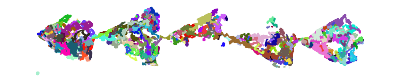

```mathematica
sampleOld = tracks//Values;
Length[sampleOld]
Show[
Graphics[ {RandomColor[], Line[ #[[All, {2,3}]]]} &/@ sampleOld ],
ImageSize->Full
]
```